## C = 1

```mathematica
DSolve[y'[x]==Sin[x] y[x],y[x],x]
```

{{y[x]→ⅇ^(-Cos[x]) C[1]}}

```mathematica
Exp[Integrate[Sin[x],{x,0,2π}]]
```

1

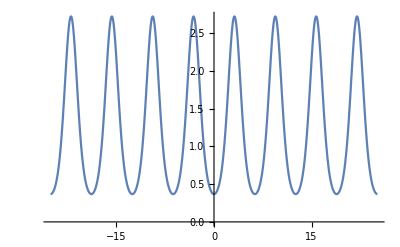

```mathematica
Plot[Exp[-Cos[θ]],{θ,-8π,8π}]
```

## C > 1

```mathematica
DSolve[y'[x]==(1/(3π)+Sin[2x]) y[x],y[x],x]
```

{{y[x]→ⅇ^(x/(3 π)-1/2 Cos[2 x]) C[1]}}

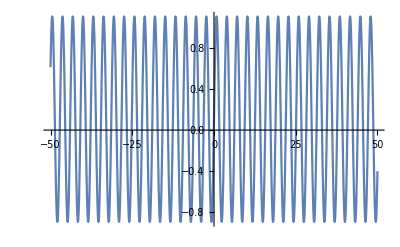

```mathematica
Plot[(1/(3π)+Sin[2x]),{x,-50,50}]
```

```mathematica
(2π)/2
```

π

```mathematica
Exp[Integrate[(1/(3π)+Sin[2x]),{x,0,π}]]
```

ⅇ^(1/3)

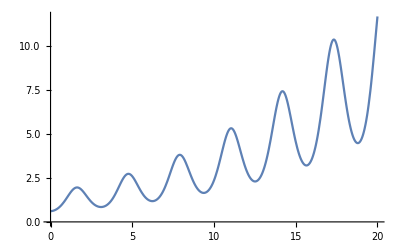

```mathematica
Plot[ⅇ^(x/(3 π)-1/2 Cos[2 x]),{x,0,20}]
```

## C > 1

```mathematica
DSolve[y'[x]==(-1/(3π)+Sin[2x]) y[x],y[x],x]
```

{{y[x]→ⅇ^(-x/(3 π)-1/2 Cos[2 x]) C[1]}}

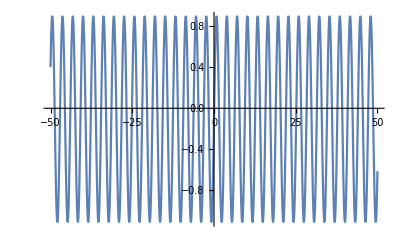

```mathematica
Plot[(-1/(3π)+Sin[2x]),{x,-50,50}]
```

```mathematica
(2π)/2
```

π

```mathematica
Exp[Integrate[(-1/(3π)+Sin[2x]),{x,0,π}]]
```

1/ⅇ^(1/3)

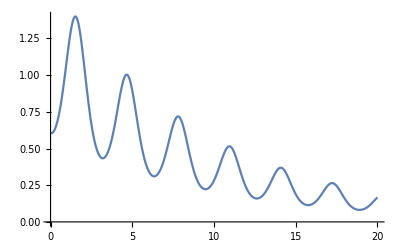

```mathematica
Plot[ⅇ^(-x/(3 π)-1/2 Cos[2 x]),{x,0,20}]
```